```mathematica
assumptions=R∈Integers&&R>=2&&A>0&&σ>0&&Ts>0
```

R∈ℤ&&R≥2&&A>0&&σ>0&&Ts>0

```mathematica
paramValues=Association[{A->1,σ->1/10,Ts->1/80,R->2}]
```

<|A→1,σ→1/10,Ts→1/80,R→2|>

```mathematica
x[A_,σ_,t_]=A*Exp[-t^2/(2σ^2)]
```

A ⅇ^(-t^2/(2 σ^2))

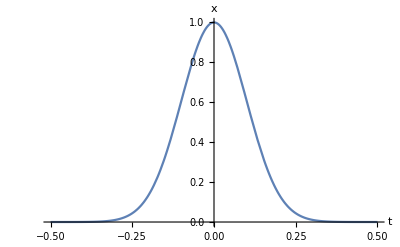

```mathematica
Block[{A,σ},{A,σ}={A,σ}/.paramValues;Plot[x[A,σ,t],{t,-5σ,5σ},AxesLabel->{"t","x"}]]
```

```mathematica
X[A_,σ_,ω_]=Assuming[assumptions,FourierTransform[x[A,σ,t],t,ω]]
```

A ⅇ^(-1/2 σ^2 ω^2) σ

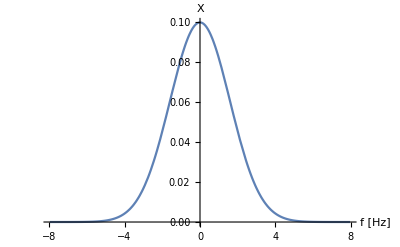

```mathematica
Block[{A,σ},{A,σ}={A,σ}/.paramValues;Plot[X[A,σ,2Pi*f],{f,-(5/σ)/(2Pi),(5/σ)/(2Pi)},AxesLabel->{"f [Hz]","X"}]]
```

```mathematica
xd[A_,σ_,Ts_,n_]=x[A,σ,n*Ts]
```

A ⅇ^(-(n^2 Ts^2)/(2 σ^2))

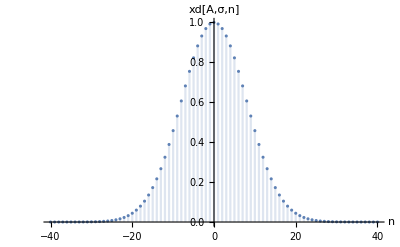

```mathematica
Block[{A,σ,Ts},{A,σ,Ts}={A,σ,Ts}/.paramValues;DiscretePlot[xd[A,σ,Ts,n],{n,-5σ/Ts,5σ/Ts},AxesLabel->{"n","xd[A,σ,n]"}]]
```

```mathematica
yd[A_,σ_,Ts_,R_,n_]=xd[A,σ,Ts,n*R]
```

A ⅇ^(-(n^2 R^2 Ts^2)/(2 σ^2))

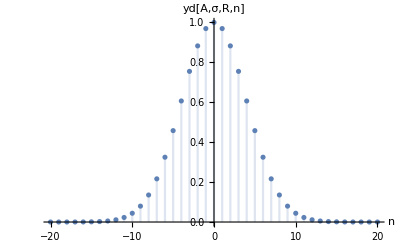

```mathematica
Block[{A,σ,Ts,R},{A,σ,Ts,R}={A,σ,Ts,R}/.paramValues;DiscretePlot[yd[A,σ,Ts,R,n],{n,-5σ/(R*Ts),5σ/(R*Ts)},AxesLabel->{"n","yd[A,σ,R,n]"}]]
```

```mathematica
Xd[A_,σ_,Ts_,ω_]:=Block[{N1=5σ/Ts},Sum[xd[A,σ,Ts,n]Exp[-I*ω*n*Ts],{n,-N1,N1}]]
```

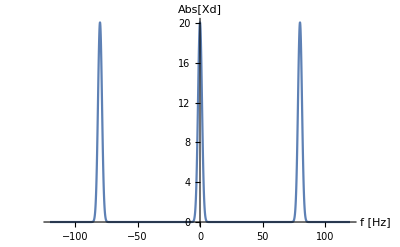

```mathematica
Block[{A,σ,Ts},{A,σ,Ts}={A,σ,Ts}/.paramValues;Plot[Abs[Xd[A,σ,Ts,2Pi*f]],{f,-3/2/Ts,3/2/Ts},PlotRange->Full,AxesLabel->{"f [Hz]","Abs[Xd]"}]]
```

```mathematica
Yd[A_,σ_,Ts_,R_,ω_]:=Block[{N1=5σ/(R*Ts)},Sum[yd[A,σ,Ts,R,n]Exp[-I*ω*n*R*Ts],{n,-N1,N1}]]
```

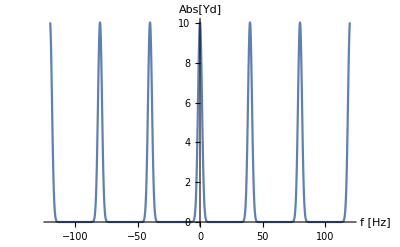

```mathematica
Block[{A,σ,Ts,R},{A,σ,Ts,R}={A,σ,Ts,R}/.paramValues;Plot[Abs[Yd[A,σ,Ts,R,2Pi*f]],{f,-3/2/Ts,3/2/Ts},PlotRange->Full,AxesLabel->{"f [Hz]","Abs[Yd]"}]]
```